```mathematica
Get[FileNameJoin[{NotebookDirectory[], "functions.m"}]]
```

```mathematica
b1 = MergeDirections["1_Danestone_RGU.txt", "1_RGU_Danestone.txt"];
b2 = MergeDirections["2_Ashwood_RGU.txt", "2_RGU_Ashwood.txt"];
b3 = MergeDirections["3_Cove_Mastrick.txt", "3_Mastrick_Cove.txt"];
b11 = MergeDirections["11_Northfield_Woodend.txt", "11_Woodend_Northfield.txt"];
b12 = MergeDirections["12_Heathryfold_Torry.txt", "12_Torry_Heathryfold.txt"];
b13 = MergeDirections["13_Golf_Links_Scatterburn.txt", "13_Scatterburn _Golf_Links.txt"];
b15 = MergeDirections["15_Balnagask_Circle_Countesswells.txt", "15_Countesswells_Balnagask_Circle.txt"];
b17 = MergeDirections["17_Dyce_Faulds_Gate.txt", "17_Faulds_Gate_Dyce.txt"];
b18 = MergeDirections["18_Dyce_Redmoss.txt", "18_Redmoss_Dyce.txt"];
b19 = MergeDirections["19_Culter_Tillydrone.txt", "19_Tillydrone_Culter.txt"];
b20 = MergeDirections["20_Guild_str_Hillhead.txt", "20_Hillhead_Guild_str.txt"];
b23 = MergeDirections["23_Raasay_Gardens_Heathryfold.txt",  "23_Heathryfold_Raasay_Gardens.txt"];
```

```mathematica
buses = {b11, b19};
routeNames = {"11", "19"};
```

```mathematica
TAPs=Algorithm821[buses, routeNames];
```

```mathematica
mtx =MatrixFromPetriNet[TAPs[[1]], TAPs[[2]], TAPs[[3]]];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

```mathematica
Dimensions[mtx]
```

{22,22}

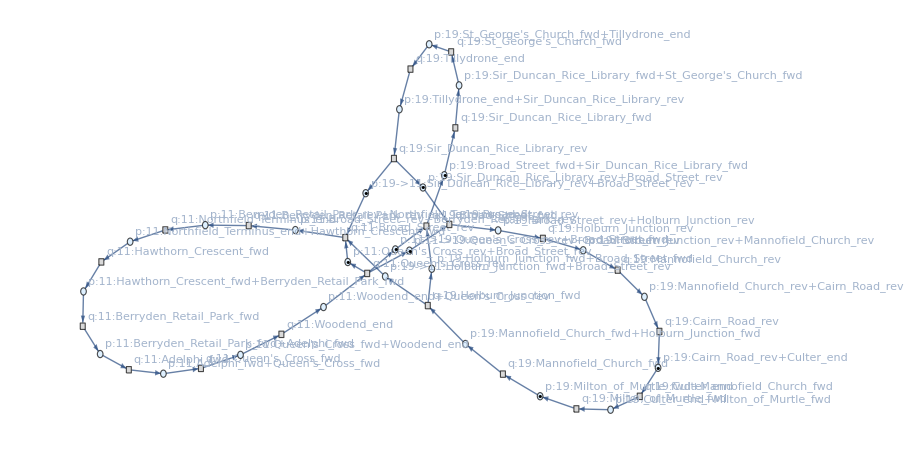

```mathematica
CreatePetriNetFromTAPs[TAPs]
```

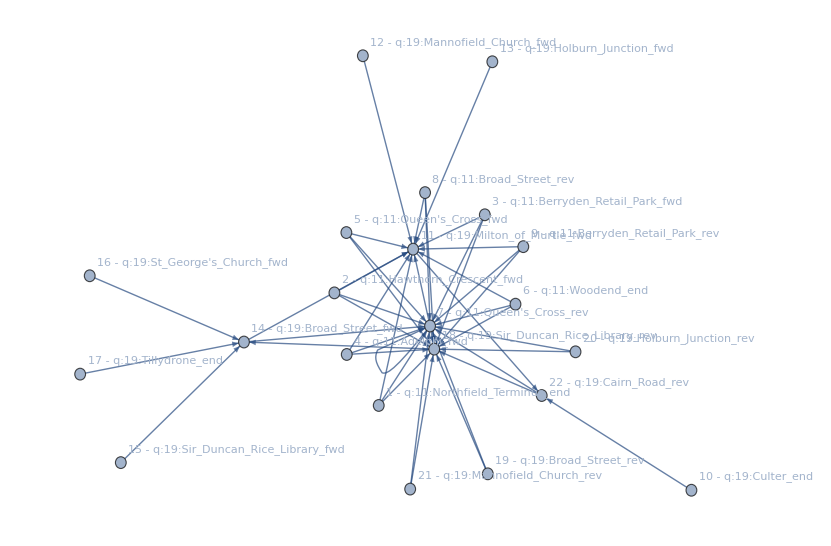

```mathematica
MakeAdjacencyGraph[mtx, TAPs]
```

```mathematica
mtx // MatrixForm
```

(-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 33. | -∞ | -∞ | -∞ | 56. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 38. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 41. | -∞ | -∞ | -∞ | 64. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 46. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 50. | -∞ | -∞ | -∞ | 73. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 55. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 61. | -∞ | -∞ | -∞ | 84. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 66. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 73. | -∞ | -∞ | -∞ | 96. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 78. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 81. | -∞ | -∞ | -∞ | 104. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 86. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 89. | -∞ | -∞ | -∞ | 112. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 94. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | 33. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 21. | -∞ | -∞ | -∞ | 44. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 26. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 13.
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 27.
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 24. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | 33. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 14. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 17. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 20. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 28. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 17. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 22. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 28. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 33. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 39. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 44. | -∞ | -∞ | -∞ | -∞)

```mathematica
TimeObject[{0,#,0}] &/@ xnext
```

{00:57:00TimeObject[{0,57,0.},Instant],01:05:00TimeObject[{1,5,0.},Instant],01:14:00TimeObject[{1,14,0.},Instant],01:25:00TimeObject[{1,25,0.},Instant],01:37:00TimeObject[{1,37,0.},Instant],01:45:00TimeObject[{1,45,0.},Instant],01:53:00TimeObject[{1,53,0.},Instant],00:34:00TimeObject[{0,34,0.},Instant],00:45:00TimeObject[{0,45,0.},Instant],TimeObject[{0,-∞,0}],TimeObject[{0,-∞,0}],00:16:00TimeObject[{0,16,0.},Instant],00:25:00TimeObject[{0,25,0.},Instant],00:34:00TimeObject[{0,34,0.},Instant],TimeObject[{0,-∞,0}],TimeObject[{0,-∞,0}],TimeObject[{0,-∞,0}],TimeObject[{0,-∞,0}],00:15:00TimeObject[{0,15,1.13687×10^-13},Instant],00:22:00TimeObject[{0,22,0.},Instant],00:33:00TimeObject[{0,33,0.},Instant],00:44:00TimeObject[{0,44,0.},Instant]}

```mathematica
v = MakeStateVector[mtx]
```

{-∞,-∞,-∞,-∞,-∞,-∞,0,-∞,-∞,-∞,0,-∞,-∞,0,-∞,-∞,-∞,0,-∞,-∞,-∞,0}

```mathematica
ttb = TimeTable[mtx,v, TAPs[[1]]];
```

```mathematica
ttb // Transpose // MatrixForm
```

(q:11:Northfield_Terminus_end | 56.
q:11:Hawthorn_Crescent_fwd | 64.
q:11:Berryden_Retail_Park_fwd | 73.
q:11:Adelphi_fwd | 84.
q:11:Queen's_Cross_fwd | 96.
q:11:Woodend_end | 104.
q:11:Queen's_Cross_rev | 112.
q:11:Broad_Street_rev | 33.
q:11:Berryden_Retail_Park_rev | 44.
q:19:Culter_end | 13.
q:19:Milton_of_Murtle_fwd | 27.
q:19:Mannofield_Church_fwd | 15.
q:19:Holburn_Junction_fwd | 24.
q:19:Broad_Street_fwd | 33.
q:19:Sir_Duncan_Rice_Library_fwd | 14.
q:19:St_George's_Church_fwd | 17.
q:19:Tillydrone_end | 20.
q:19:Sir_Duncan_Rice_Library_rev | 28.
q:19:Broad_Street_rev | 15.
q:19:Holburn_Junction_rev | 22.
q:19:Mannofield_Church_rev | 33.
q:19:Cairn_Road_rev | 44.)

```mathematica
SplitByRoutes[ttb, routeNames][[2]] //MatrixForm
```

(q:19:Culter_end | 13.
q:19:Milton_of_Murtle_fwd | 27.
q:19:Mannofield_Church_fwd | 15.
q:19:Holburn_Junction_fwd | 24.
q:19:Broad_Street_fwd | 33.
q:19:Sir_Duncan_Rice_Library_fwd | 14.
q:19:St_George's_Church_fwd | 17.
q:19:Tillydrone_end | 20.
q:19:Sir_Duncan_Rice_Library_rev | 28.
q:19:Broad_Street_rev | 15.
q:19:Holburn_Junction_rev | 22.
q:19:Mannofield_Church_rev | 33.
q:19:Cairn_Road_rev | 44.)